```mathematica
xplane = InfinitePlane[{{0,0,0},{0,0,1},{0,1,0}}]
yplane = InfinitePlane[{{0,0,0},{0,0,1},{1,0,0}}]
zplane = InfinitePlane[{{0,0,0},{1,0,0},{0,1,0}}]
```

InfinitePlane[{{0,0,0},{0,0,1},{0,1,0}}]

InfinitePlane[{{0,0,0},{0,0,1},{1,0,0}}]

InfinitePlane[{{0,0,0},{1,0,0},{0,1,0}}]

```mathematica
FigureXYZslice=SliceVectorPlot3D[{x y-y z-y,x-x y,y z-z},{yplane,xplane,zplane},{y,0,4},{x,0,4},{z,0,4},
VectorScale->{Tiny,Automatic,None},
VectorColorFunction->"DarkRainbow",
Ticks->None,
AxesLabel->
{Style["y",FontSize->24],Style["x",FontSize->24],Style["z",FontSize->24]},
Boxed->False,
PlotTheme->"Monochrome",
PerformanceGoal->"Quality",
ViewPoint->{1.5,1.6,1}]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["XYZ.pdf",FigureXYZslice,"PDF"]
```

C:\Users\Admin\Documents\GitHub\AMATH383Paper

XYZ.pdf

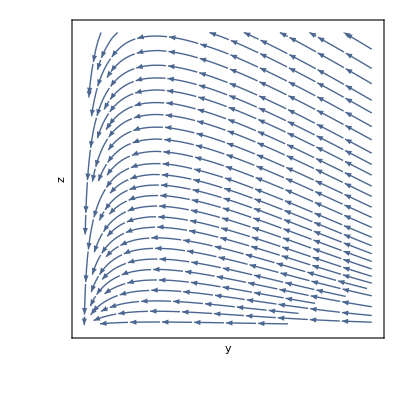

```mathematica
FigureYZplane=StreamPlot[{-y*z-y,y*z-z},{y,0,4},{z,0,4},
FrameLabel->{Style["y",FontSize->24,FontColor->Black],Style["z",FontSize->24,FontColor->Black]},
RotateLabel->False,
PerformanceGoal->"Quality",
FrameTicks->None,
StreamScale->{0.1,.7,None}]
```

```mathematica
Export["YZ.pdf",FigureYZplane,"PDF"]
```

YZ.pdf

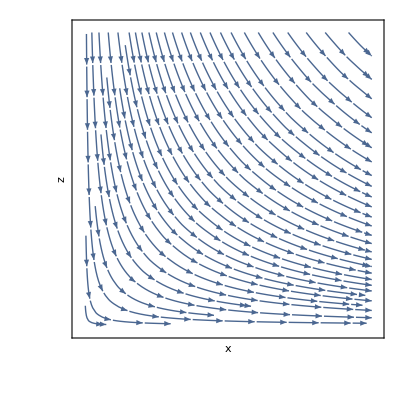

```mathematica
FigureXZplane=StreamPlot[{x,-z},{x,0,4},{z,0,4},
FrameLabel->{Style["x",FontSize->24,FontColor->Black],Style["z",FontSize->24,FontColor->Black]},
RotateLabel->False,
PerformanceGoal->"Quality",
FrameTicks->None,
StreamScale->{0.1,.7,None}]
```

```mathematica
Export["XZ.pdf",FigureXZplane,"PDF"]
```

XZ.pdf

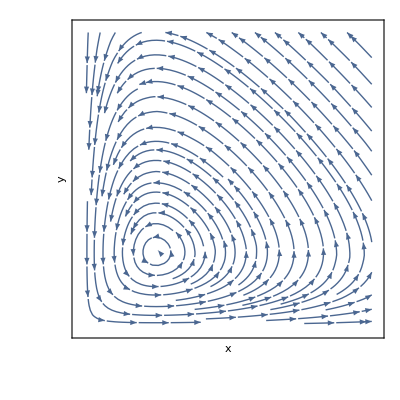

```mathematica
FigureXYplane=StreamPlot[{x-x*y,x*y-y},{x,0,4},{y,0,4},
FrameLabel->{Style["x",FontSize->24,FontColor->Black],Style["y",FontSize->24,FontColor->Black]},
RotateLabel->False,
PerformanceGoal->"Quality",
FrameTicks->None,
StreamScale->{0.1,.7,None}]
```

```mathematica
Export["XY.pdf",FigureXYplane,"PDF"]
```

XY.pdf

```mathematica
Clear[x,y,z,t]
Clear[Derivative]
s=NDSolve[{x'[t]==x[t]-x[t]*y[t],y'[t]==x[t]*y[t]-y[t]*z[t]-y[t],z'[t]==y[t]*z[t]-z[t],x[0]==1.4,y[0]==1,z[0]==1},{x,y,z},{t,0,10},MaxSteps->Infinity]
p1=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.s],{t,0,4},PlotPoints->100,PlotStyle->Gray,PlotRange->{{1,3},{0,2},{0,2}},ViewPoint->{1,3,0}]
par1=Plot[{
Callout[x[t]/. s,"x(t)",Above,LabelStyle->Directive[Medium]],
Callout[y[t]/. s,"y(t)",Above,LabelStyle->Directive[Medium]],
Callout[z[t]/. s,"z(t)",Above,LabelStyle->Directive[Medium]]},
{t,0,10},PlotRange->{0,3},PlotStyle->Gray,AxesLabel->{t,"Population"}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

-Graphics3D-

par1.pdf

```mathematica
Clear[x,y,z,t]
Clear[Derivative]
s=NDSolve[{x'[t]==x[t]-x[t]*y[t],y'[t]==x[t]*y[t]-y[t]*z[t]-y[t],z'[t]==y[t]*z[t]-z[t],x[0]==1.6,y[0]==1,z[0]==1},{x,y,z},{t,0,10},MaxSteps->Infinity]
p2=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.s],{t,0,6},PlotPoints->100,PlotStyle->Brown,PlotRange->{{1,3},{0,2},{0,2}},ViewPoint->{1,3,0}]
Plot[{
Callout[x[t]/. s,"x(t)",Above,LabelStyle->Directive[Medium]],
Callout[y[t]/. s,"y(t)",Above,LabelStyle->Directive[Medium]],
Callout[z[t]/. s,"z(t)",Above,LabelStyle->Directive[Medium]]},
{t,0,10},PlotRange->{0,3},PlotStyle->Brown,AxesLabel->{t,"Population"}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

-Graphics3D-

```mathematica
Clear[x,y,z,t]
Clear[Derivative]
s=NDSolve[{x'[t]==x[t]-x[t]*y[t],y'[t]==x[t]*y[t]-y[t]*z[t]-y[t],z'[t]==y[t]*z[t]-z[t],x[0]==1.8,y[0]==1,z[0]==1},{x,y,z},{t,0,10},MaxSteps->Infinity]
p3=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.s],{t,0,10},PlotPoints->100,PlotStyle->Orange,ViewPoint->{1,3,0},PlotRange->{{1,3},{0,2},{0,2}}]
Plot[{
Callout[x[t]/. s,"x(t)",Above,LabelStyle->Directive[Medium]],
Callout[y[t]/. s,"y(t)",Above,LabelStyle->Directive[Medium]],
Callout[z[t]/. s,"z(t)",Above,LabelStyle->Directive[Medium]]},
{t,0,10},PlotRange->{0,3},PlotStyle->Orange,AxesLabel->{t,"Population"}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

-Graphics3D-

-Graphics-

```mathematica
Show[p1,p2,p3]
LineLegend[{Orange,Brown,Gray},{"x(0)=1.4, y(0)=1, z(0)=1","x(0)=1.6, y(0)=1, z(0)=1","x(0)=1.8, y(0)=1, z(0)=1"}]
```

-Graphics3D-